```mathematica
ClearAll["Global`*"]
```

# CSC Matrix Tester

## Generate rect CSC matrix in CATSPDEs sparse format

### Set input data

```mathematica
rows=5; (* numb of rows *)
cols=10; (* ″ cols *)
sparsity=.6; (* % of zero elements *)
```

### Compute sparse matrix A and vectors u, v for multiplications by A.u, A^T.v

```mathematica
nnzeros=Round[(1-sparsity) rows cols];
coords=Table[{RandomInteger@{1,rows},RandomInteger@{1,cols}}-> RandomInteger@{1,20},{i,nnzeros}];
A=SparseArray[coords,{rows,cols}];
```

```mathematica
u=Table[RandomInteger@{1,20},{i,cols}]; 
v=Table[RandomInteger@{1,20},{i,rows}];
```

```mathematica
A//MatrixForm
```

(14 | 0 | 14 | 0 | 0 | 0 | 0 | 1 | 0 | 17
0 | 11 | 0 | 8 | 0 | 0 | 9 | 12 | 8 | 9
0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 3 | 0
17 | 1 | 0 | 6 | 0 | 0 | 4 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
jptr={0}; (* column pointers *)
iptr={}; (* row indicies *)
mval={}; (* values *)
Do[
k=jptr[[j]];
Do[
If[
A[[i,j]]≠0,
++k;
AppendTo[mval,A[[i,j]]];
AppendTo[iptr,i-1]
],
{i,rows}
];
AppendTo[jptr,k],
{j,cols}
]
```

### Export data

```mathematica
SetDirectory[NotebookDirectory[]<>"output/CSC"];
Export["A.dat",{
{rows,cols,jptr[[-1]]},
jptr,
iptr,
mval
}];
Export["u.dat",u];
Export["v.dat",v];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../HarwellBoeing"];
Export["mathematica.rra",A,"HarwellBoeing"];
```

### Check multiplication results

Output vectors should be zeros!

```mathematica
SetDirectory[NotebookDirectory[]<>"../output/CSC"];
```

```mathematica
AxU=Import["AxU.dat","List","LineSeparators"->{" "},"IgnoreEmptyLines"->True];
MatrixForm[AxU-A.u]
```

(0.
0.
0.
0.
0.)

```mathematica
AxV=Import["AxV.dat","List","LineSeparators"->{" "},"IgnoreEmptyLines"->True];
MatrixForm[AxV-Transpose@A.v]
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

## Harwell–Boeing

```mathematica
matrixName="mathematica.rra"; (* mathematica.rra, illc1033.rra, e40r5000.rua, qc2534.cua *)
```

### Load from original HB–collection

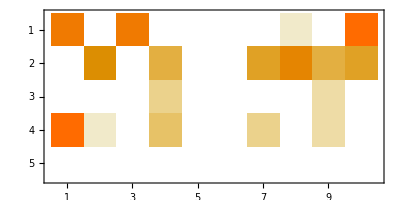

```mathematica
SetDirectory[NotebookDirectory[]<>"../HarwellBoeing"];
M=Import[matrixName];
MatrixPlot@M
```

### Load from CATSPDEs output

```mathematica
SetDirectory[NotebookDirectory[]<>"../output/CSC/HarwellBoeing"];
P=Import[matrixName];
MatrixPlot@P
```

-Graphics-

### Compare results

```mathematica
M[[1,2]]
P[[1,2]]
MatrixPlot[M-P]
```

0

0

-Graphics-